```mathematica
F= {{0,-E1,-E2,-E3},{E1,0,B3,-B2},{E2,-B3,0,B1},{E3,B2,-B1,0}}
```

```mathematica
{{0,-E1,-E2,-E3},{E1,0,B3,-B2},{E2,-B3,0,B1},{E3,B2,-B1,0}}//MatrixForm
```

(0 | -E1 | -E2 | -E3
E1 | 0 | B3 | -B2
E2 | -B3 | 0 | B1
E3 | B2 | -B1 | 0)

```mathematica
η = {{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
F1 = η.F //MatrixForm
```

(0 | E1 | E2 | E3
E1 | 0 | B3 | -B2
E2 | -B3 | 0 | B1
E3 | B2 | -B1 | 0)

```mathematica
F2 = η.F.η //MatrixForm
```

(0 | E1 | E2 | E3
-E1 | 0 | B3 | -B2
-E2 | -B3 | 0 | B1
-E3 | B2 | -B1 | 0)

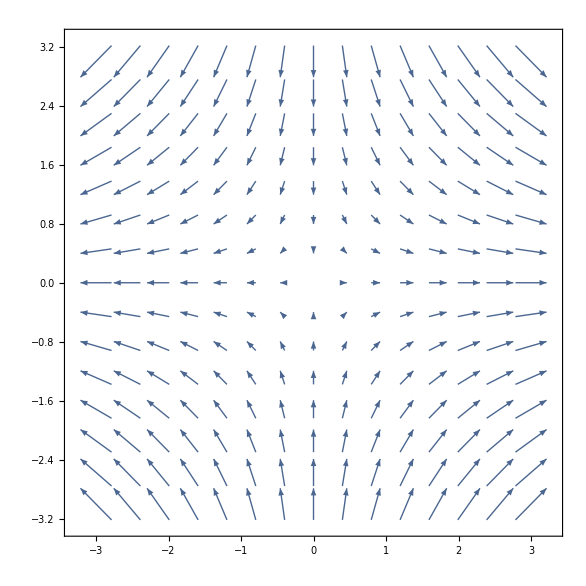

```mathematica
VectorPlot[{2t,-2x},{t,-3,3},{x,-3,3}]
```